```mathematica
plotSolution[net_,t_]:=Show[net@Range[-3,3,.02],Red],Epilog->Text[t,{10,0.9},{-1,0}]]
```

```mathematica
net=NetInitialize[NetChain[{LinearLayer[1]},"Input"->1]];
gradientNorms[assoc_]:=BarChart[Log[Max[Abs[#]]]&/@assoc,ChartLabels->Automatic,BarOrigin->Right];
```

```mathematica
model=NetTrain[net,format/@datum,MaxTrainingRounds->Quantity[30,"Seconds"],TrainingProgressReporting->{Function[tune[#Net]],"Interval"->Quantity[1,"Seconds"]}];
params=NetExtract[model,{{All,"Weights"},{All,"Biases"}}]//Flatten;
```

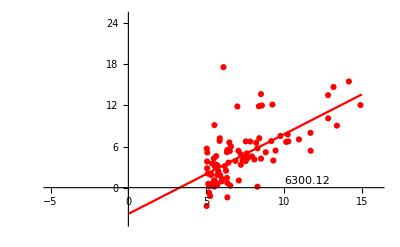

```mathematica
tune@@params
```

```mathematica
haha
```

```mathematica
tune@@params
```

-Graphics-

how about a simple predictor that overfits!

## let the neural network calculate its own line

```mathematica
error[w_,b_]:=Total[Function[{x,y},(y-w x+b)^2]@@#&/@datum]
tune[w_,b_]:=Show[plot[datum],Plot[x w+b,{x,0,15},PlotRange->{{-5,16},{-5,25}},PlotStyle->Red],Epilog->Text[error[w,b],{10,0.9},{-1,0}]]
```

```mathematica
Range[-5,10,.1]
```

{-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
Thread[List[]]
```

```mathematica
tune[f_]:=(r=Range[-5,15,.1];Show[plot[datum~Join~Thread[{r,First[f@#]&/@r}]]])
```

```mathematica
error[f_]:=Total[Module[{},
point=#;
{x,y}=point;
(y-First[f[x]])^2
]&/@datum]
```

```mathematica
error[net]
```

7199.79

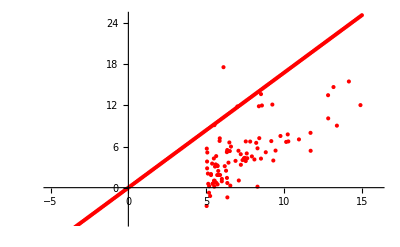

```mathematica
tune[net]
```

```mathematica
error[net]
```

7199.79